```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
ϵ=10^-15;(*λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0]*);q=k;
U[G_]:=G^2/12;a=1/(√6);
W[z_]:=k (E^(a ϕ[z])(U[G[z]]+1-a ϕ[z])-1);
Vt[z_]:=6 k^2 (2+ⅇ^(2 a ϕ[z]) (-2+(U[G[z]]-a ϕ[z]) (-4+(-2+3 a^2) (U[G[z]]-a ϕ[z]))+3 U'[G[z]]^2));
dVtdϕ[z_]:=12 a ⅇ^(2 a ϕ[z]) k^2 ((U[G[z]]-a ϕ[z]) (-2-3 a^2+(-2+3 a^2) (U[G[z]]-a ϕ[z]))+3 U'[G[z]]^2);
dVtdG[z_]:=-12 ⅇ^(2 a ϕ[z]) k^2 U'[G[z]] (2+(-2+3 a^2) (-U[G[z]]+a ϕ[z])-3 U''[G[z]]);
eqn1=3 E^(a ϕ[z])(k z+1)D[(B[z]+q),z]-12(B[z]+q)^2==Vt[z]-12 k^2;
eqn2=B'[z]==E^(a ϕ[z])(k z+1)1/6(ϕ'[z]^2+G'[z]^2);
eqn3=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)ϕ'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)ϕ'[z]==dVtdϕ[z];
eqn4=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)G'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)G'[z]==dVtdG[z];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
ic6=B[ϵ]==W[ϵ];
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
WExact[z_]:=k (E^(a ϕExact[z])(U[GExact[z]]+1-a ϕExact[z])-1);
```

```mathematica
sol=First[{ϕ,G,B}/.NDSolve[{eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6},{ϕ,G,B},{z,ϵ,2/k}]];
{zmin,zmax}=First[sol[[1]]["Domain"]];
```

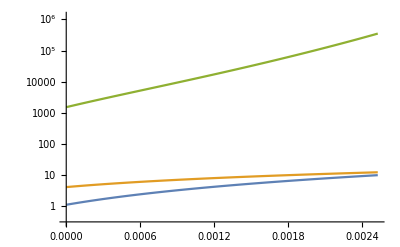

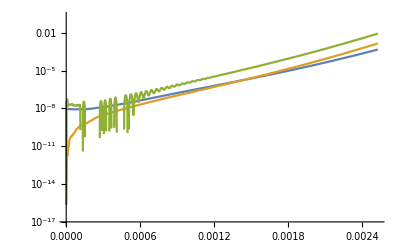

```mathematica
LogPlot[{sol[[1]][z],sol[[2]][z],sol[[3]][z]},{z,zmin,zmax},PlotRange->All]
LogPlot[{(sol[[1]][z])/ϕExact[z]-1,(sol[[2]][z])/GExact[z]-1,(sol[[3]][z])/WExact[z]-1},{z,zmin,zmax},PlotRange->All]
```

```mathematica
(*This is just to check that the analytic solutions works.  It does.*)
Block[{ϕ,G,B},
U[G_]:=G^2/12;
ϕ[z_]:=√(8/3)λ(z+1/k)^2;
G[z_]:=√(24λ)(z+1/k);
q=k;a=1/√6;
B[z_]:=k (E^(a ϕ[z])(U[G[z]]+1-a ϕ[z])-1);
Vt[z_]:=6 k^2 (2+ⅇ^(2 a ϕ[z]) (-2+(U[G[z]]-a ϕ[z]) (-4+(-2+3 a^2) (U[G[z]]-a ϕ[z]))+3 U'[G[z]]^2));
dVtdϕ[z_]:=12 a ⅇ^(2 a ϕ[z]) k^2 ((U[G[z]]-a ϕ[z]) (-2-3 a^2+(-2+3 a^2) (U[G[z]]-a ϕ[z]))+3 U'[G[z]]^2);
dVtdG[z_]:=-12 ⅇ^(2 a ϕ[z]) k^2 U'[G[z]] (2+(-2+3 a^2) (-U[G[z]]+a ϕ[z])-3 U''[G[z]]);
eqn1=3 E^(a ϕ[z])(k z+1)D[(B[z]+q),z]-12(B[z]+q)^2==Vt[z]-12 k^2;
eqn2=B'[z]==E^(a ϕ[z])(k z+1)1/6(ϕ'[z]^2+G'[z]^2);
eqn3=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)ϕ'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)ϕ'[z]==dVtdϕ[z];
eqn4=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)G'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)G'[z]==dVtdG[z];
eqn4//FullSimplify
]
```

True

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
ϵ=10^-15;(*λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];*)q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
f[z_]:=1;(*for checking analytic vacuum solution*)

eqn1=3(k z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(k z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(k z+1)(ϕ'[z])^2+(k-4β[z])ϕ'[z]+(k z+1)ϕ''[z])+(k z+1)f'[z]ϕ'[z]==1/(k z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(k z+1)ϕ'[z]G'[z]+(k-4β[z])G'[z]+(k z+1)G''[z])+(k z+1)f'[z]G'[z]==1/(k z+1)dςdG[ϕ[z],G[z]];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
```

```mathematica
βExact[z]//FullSimplify
βExact[z]//.{λ->Rationalize[638.5^2,0],k->Rationalize[1.2383 √λ,0],z->1/k,δ->10^-1}//N
(15813091 (1+1630729/3 (20000/15813091+z)^2))/20000//.{λ->Rationalize[638.5^2,0],k->Rationalize[1.2383 √λ,0],z->1/k,δ->10^-1}//N
```

k-ⅇ^(-2/3 (1/k+z)^2 λ) k δ+(4 λ)/(3 k)+(8 z λ)/3+4/3 k z^2 λ

3526.77

3540.66

```mathematica
sol=First[{ϕ,G,β}/.NDSolve[{eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic6},{ϕ,G,β},{z,ϵ,1},AccuracyGoal->∞,WorkingPrecision->75,MaxSteps->∞,Method->"StiffnessSwitching"]];
{zmin,zmax}=First[sol[[1]]["Domain"]];
```

NDSolve::ndsz: At z == 0.00889830491317725997227104081248226518354203355160176887730060078013927213799, step size is effectively zero; singularity or stiff system suspected.

```mathematica
k zmax
sol[[1]][zmax]
sol[[2]][zmax]
sol[[3]][zmax]
```

7.03548526689095555360897225162479976167409394382659835088611172455066514959

135.

253.9

6.1×10^74

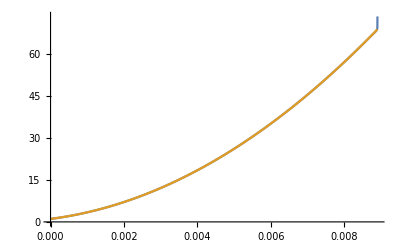

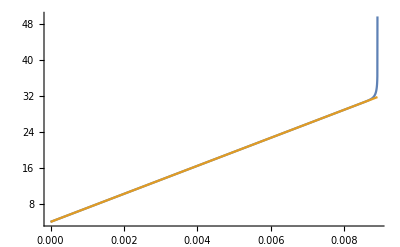

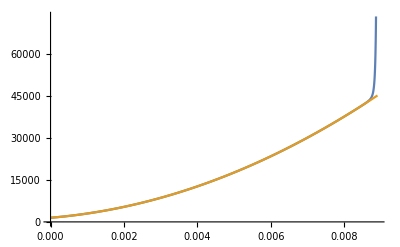

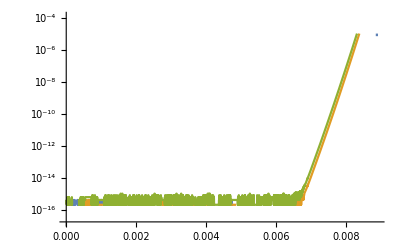

```mathematica
Plot[{sol[[1]][z],ϕExact[z]},{z,zmin,zmax}]
Plot[{sol[[2]][z],GExact[z]},{z,zmin,zmax}]
Plot[{sol[[3]][z],βExact[z]},{z,zmin,zmax}]
LogPlot[{(sol[[1]][z])/ϕExact[z]-1,(sol[[2]][z])/GExact[z]-1,(sol[[3]][z])/βExact[z]-1},{z,zmin,zmax}]
```

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];

(*W[ϕ_,G_]:=k (E^(a ϕ)(U[G]+1-a ϕ)-1);*)
W[ϕ_,G_]:=E^(a ϕ)Ω[ϕ,G];
Vt[ϕ_,G_]:=18((D[W[ϕ,G], ϕ])^2+(D[W[ϕ,G], G])^2)-12 W[ϕ,G]^2-24 k W[ϕ,G];
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] E^(-a ϕ);
dVtdϕ[ϕ_,G_]:=12 a ⅇ^(2 a ϕ[z]) k^2 ((U[G[z]]-a ϕ[z]) (-2-3 a^2+(-2+3 a^2) (U[G[z]]-a ϕ[z]))+3 U'[G[z]]^2);
dVtdG[ϕ_,G_]:=-12 ⅇ^(2 a ϕ[z]) k^2 U'[G[z]] (2+(-2+3 a^2) (-U[G[z]]+a ϕ[z])-3 U''[G[z]]);
Vt[ϕ[z],G[z]]==E^(2a ϕ[z])ς[ϕ[z],G[z]]//FullSimplify
dVtdϕ[ϕ[z],G[z]]
```

True

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
B[z_]:=E^(a ϕ[z])β[z]-q;
f[z_]:=1;
eqn1=3 E^(a ϕ[z])(k z+1)D[(B[z]+q),z]-12(B[z]+q)^2==E^(2a ϕ[z])ς[ϕ[z],G[z]]-12 k^2;
eqn2=B'[z]==E^(a ϕ[z])(k z+1)1/6(ϕ'[z]^2+G'[z]^2);
eqn3=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)ϕ'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)ϕ'[z]==D[E^(2a ϕ[z])ς[ϕ[z],G[z]],ϕ[z]];
eqn4=E^(a ϕ[z])(k z+1)D[E^(a ϕ[z])(k z+1)G'[z],z]-4(B[z]+q)E^(a ϕ[z])(k z+1)G'[z]==D[E^(2a ϕ[z])ς[ϕ[z],G[z]],G[z]];
eqn1C=3(k z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-12 E^(-2a ϕ[z])k^2;
eqn2C=6(a ϕ'[z]β[z]+β'[z])==(k z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3C=f[z](a(k z+1)(ϕ'[z])^2+(k-4β[z])ϕ'[z]+(k z+1)ϕ''[z])+(k z+1)f'[z]ϕ'[z]==1/(k z+1)(2a ς[ϕ[z],G[z]]+D[ς[ϕ[z],G[z]],ϕ[z]]);
eqn4C=f[z](a(k z+1)ϕ'[z]G'[z]+(k-4β[z])G'[z]+(k z+1)G''[z])+(k z+1)f'[z]G'[z]==1/(k z+1)D[ς[ϕ[z],G[z]],G[z]];
ⅇ^(-2 a ϕ[z])eqn1[[1]]-eqn1C[[1]]==ⅇ^(-2 a ϕ[z])eqn1[[2]]-eqn1C[[2]]//FullSimplify
6 ⅇ^(-a ϕ[z])eqn2[[1]]-eqn2C[[1]]==6 ⅇ^(-a ϕ[z])eqn2[[2]]-eqn2C[[2]]//FullSimplify
eqn3//FullSimplify;
eqn3C//FullSimplify;
2 a ς[ϕ[z],G[z]]+(1+k z) (-ϕ'[z] (k-4 β[z]+a (1+k z) ϕ'[z])-(1+k z) ϕ''[z])+Derivative[1,0][ς][ϕ[z],G[z]]==2 a ς[ϕ[z],G[z]]+Derivative[1,0][ς][ϕ[z],G[z]]-(k z+1)(ϕ'[z] (k-4 β[z]+(a+a k z) ϕ'[z])+ϕ''[z]+k z ϕ''[z])//FullSimplify
eqn4//FullSimplify;
eqn4C//FullSimplify;
-((1+k z) G'[z] (k-4 β[z]+a (1+k z) ϕ'[z])+(1+k z)^2 G''[z]-Derivative[0,1][ς][ϕ[z],G[z]])==Derivative[0,1][ς][ϕ[z],G[z]]-(k z+1)(G'[z] (k-4 β[z]+a (1+k z) ϕ'[z])+(1+k z) G''[z])//FullSimplify
```

True

True

True

«1 more identical outputs»